```mathematica
listOfCountries = CountryData[All];
```

```mathematica
countryList=Table[{i,CountryData[i,"Population"],CountryData[i,"LandArea"]},{i,listOfCountries}];
```

```mathematica
Short[countryList]
```

{{Afghanistan,38928341 people,652230. km^2},{Aland Islands,29013 people,1580.23 km^2},{Albania,2877800 people,27398. km^2},{Algeria,43851043 people,2.38174×10^6 km^2},{American Samoa,55197 people,199. km^2},{Andorra,77265 people,468. km^2},{Angola,32866268 people,1.2467×10^6 km^2},{Anguilla,15002 people,91. km^2},{Antigua and Barbuda,97928 people,442.6 km^2},{Argentina,45195777 people,2.73669×10^6 km^2},{Armenia,2963234 people,28203. km^2},{Aruba,106766 people,180. km^2},{Australia,25499881 people,7.6823×10^6 km^2},{Austria,9006400 people,82445. km^2},{Azerbaijan,10139175 people,82629. km^2},{Bahamas,393248 people,10010. km^2},{Bahrain,1701583 people,760. km^2},«215»,{United Arab Emirates,9890400 people,83600. km^2},{United Kingdom,67886004 people,241930. km^2},{United States,331449281 people,9.16192×10^6 km^2},{United States Minor Outlying Islands,300 people,3.9 km^2},{United States Virgin Islands,104423 people,346. km^2},{Uruguay,3473727 people,175015. km^2},{Uzbekistan,33469199 people,425400. km^2},{Vanuatu,307150 people,12189. km^2},{Vatican City,809 people,0.44 km^2},{Venezuela,28435943 people,882050. km^2},{Vietnam,97338583 people,325360. km^2},{Wallis and Futuna Islands,11246 people,142. km^2},{West Bank,2731052 people,5640. km^2},{Western Sahara,597330 people,266000. km^2},{Yemen,29825968 people,527968. km^2},{Zambia,18383956 people,743398. km^2},{Zimbabwe,14862927 people,386847. km^2}}

```mathematica
(* 通过传给CountryData第三个参数返回给定指标的单位 *)
CountryData["Afghanistan","Population","Units"]
```

People

```mathematica
CountryData["Afghanistan","LandArea","Units"]
```

SquareKilometers

```mathematica
(* 对单位进型转换 *)
UnitConvert[Quantity[1,("Kilometers")^2],"Acres"]
```

39062500000/158080329 acres

```mathematica
N[Quantity[39062500000/158080329,"Acres"]]
```

247.105 acres

```mathematica
(* 基于转换率 km^2->acres 求解人口密度 *)
Table[country[[1;;3]],{country,countryList}]
```

{{Afghanistan,38928341 people,652230. km^2},{Aland Islands,29013 people,1580.23 km^2},{Albania,2877800 people,27398. km^2},{Algeria,43851043 people,2.38174×10^6 km^2},{American Samoa,55197 people,199. km^2},{Andorra,77265 people,468. km^2},{Angola,32866268 people,1.2467×10^6 km^2},{Anguilla,15002 people,91. km^2},{Antigua and Barbuda,97928 people,442.6 km^2},{Argentina,45195777 people,2.73669×10^6 km^2},{Armenia,2963234 people,28203. km^2},{Aruba,106766 people,180. km^2},{Australia,25499881 people,7.6823×10^6 km^2},{Austria,9006400 people,82445. km^2},{Azerbaijan,10139175 people,82629. km^2},{Bahamas,393248 people,10010. km^2},{Bahrain,1701583 people,760. km^2},{Bangladesh,164689383 people,130168. km^2},{Barbados,287371 people,430. km^2},{Belarus,9449321 people,202900. km^2},{Belgium,11589616 people,30278. km^2},{Belize,397621 people,22806. km^2},{Benin,12123198 people,110622. km^2},{Bermuda,62273 people,54. km^2},{Bhutan,771612 people,38394. km^2},{Bolivia,11673029 people,1.0833×10^6 km^2},{Caribbean Netherlands,26221 people,328. km^2},{Bosnia and Herzegovina,3280815 people,51187. km^2},{Botswana,2351625 people,566730. km^2},{Bouvet Island,Missing[NoResidentPopulation],49. km^2},{Brazil,212559409 people,8.45942×10^6 km^2},{British Indian Ocean Territory,2500 people,60. km^2},{British Virgin Islands,30237 people,151. km^2},{Brunei,437483 people,5265. km^2},{Bulgaria,6948445 people,108489. km^2},{Burkina Faso,20903278 people,273800. km^2},{Burundi,11890781 people,25680. km^2},{Cambodia,16718971 people,176515. km^2},{Cameroon,26545864 people,472710. km^2},{Canada,37742157 people,9.09351×10^6 km^2},{Cape Verde,555988 people,4033. km^2},{Cayman Islands,65720 people,264. km^2},{Central African Republic,4829764 people,622984. km^2},{Chad,16425859 people,1.2592×10^6 km^2},{Chile,19116209 people,743812. km^2},{China,1439323774 people,9.32641×10^6 km^2},{Christmas Island,1513 people,135. km^2},{Cocos Keeling Islands,550 people,14. km^2},{Colombia,50882884 people,1.0387×10^6 km^2},{Comoros,869595 people,2235. km^2},{Cook Islands,17564 people,236. km^2},{Costa Rica,5094114 people,51060. km^2},{Croatia,4105268 people,55974. km^2},{Cuba,11326616 people,109820. km^2},{Curacao,164100 people,444. km^2},{Cyprus,1207361 people,9241. km^2},{Czech Republic,10708982 people,77247. km^2},{Democratic Republic of the Congo,89561404 people,2.26705×10^6 km^2},{Denmark,5792203 people,42434. km^2},{Djibouti,988002 people,23180. km^2},{Dominica,71991 people,751. km^2},{Dominican Republic,10847904 people,48320. km^2},{East Timor,1318442 people,14874. km^2},{Ecuador,17643060 people,276841. km^2},{Egypt,102334403 people,995450. km^2},{El Salvador,6486201 people,20721. km^2},{Equatorial Guinea,1402985 people,28051. km^2},{Eritrea,3546427 people,101000. km^2},{Estonia,1326539 people,42388. km^2},{Ethiopia,114963583 people,1.11968×10^6 km^2},{Falkland Islands,3483 people,12173. km^2},{Faroe Islands,48865 people,1393. km^2},{Fiji,896444 people,18274. km^2},{Finland,5540718 people,303815. km^2},{France,65273512 people,549970. km^2},{French Guiana,298682 people,89150. km^2},{French Polynesia,280904 people,3827. km^2},{French Southern And Antarctic lands,196 people,439781. km^2},{Gabon,2225728 people,257667. km^2},{Gambia,2416664 people,10000. km^2},{Gaza Strip,1763387 people,360. km^2},{Georgia,3989175 people,69700. km^2},{Germany,83783945 people,348672. km^2},{Ghana,31072945 people,227533. km^2},{Gibraltar,33691 people,6.5 km^2},{Greece,10423056 people,130800. km^2},{Greenland,56772 people,2.16609×10^6 km^2},{Grenada,112519 people,344. km^2},{Guadeloupe,400127 people,1706. km^2},{Guam,168783 people,544. km^2},{Guatemala,17915567 people,107159. km^2},{Guernsey,65605 people,78. km^2},{Guinea,13132792 people,245717. km^2},{Guinea-Bissau,1967998 people,28120. km^2},{Guyana,786559 people,196849. km^2},{Haiti,11402533 people,27560. km^2},{Honduras,9904608 people,111890. km^2},{Hong Kong,7496988 people,1054. km^2},{Hungary,9660350 people,89608. km^2},{Iceland,341250 people,100250. km^2},{India,1380004385 people,2.97319×10^6 km^2},{Indonesia,273523621 people,1.81157×10^6 km^2},{Iran,83992953 people,1.636×10^6 km^2},{Iraq,40222503 people,432162. km^2},{Ireland,4937796 people,68883. km^2},{Isle of Man,85032 people,572. km^2},{Israel,8655541 people,20330. km^2},{Italy,60461828 people,294140. km^2},{Ivory Coast,26378275 people,318003. km^2},{Jamaica,2961161 people,10831. km^2},{Japan,126476458 people,374744. km^2},{Jersey,95732 people,116. km^2},{Jordan,10203140 people,88802. km^2},{Kazakhstan,18776707 people,2.6997×10^6 km^2},{Kenya,53771300 people,569140. km^2},{Kiribati,119446 people,811. km^2},{Kosovo,1859203 people,10887. km^2},{Kuwait,4270563 people,17818. km^2},{Kyrgyzstan,6524191 people,191801. km^2},{Laos,7275556 people,230800. km^2},{Latvia,1886202 people,62249. km^2},{Lebanon,6825442 people,10282. km^2},{Lesotho,2142252 people,30355. km^2},{Liberia,5057677 people,96320. km^2},{Libya,6871287 people,1.75954×10^6 km^2},{Liechtenstein,38137 people,160. km^2},{Lithuania,2722291 people,62680. km^2},{Luxembourg,625976 people,2586. km^2},{Macau,649342 people,28.2 km^2},{North Macedonia,2083380 people,25433. km^2},{Madagascar,27691019 people,581540. km^2},{Malawi,19129955 people,94080. km^2},{Malaysia,32365998 people,328657. km^2},{Maldives,540542 people,298. km^2},{Mali,20250834 people,1.22019×10^6 km^2},{Malta,441539 people,316. km^2},{Marshall Islands,59194 people,181. km^2},{Martinique,375265 people,1060. km^2},{Mauritania,4649660 people,1.0307×10^6 km^2},{Mauritius,1271767 people,2030. km^2},{Mayotte,272813 people,374. km^2},{Mexico,128932753 people,1.94395×10^6 km^2},{Micronesia,115021 people,702. km^2},{Moldova,4033963 people,32891. km^2},{Monaco,39244 people,2. km^2},{Mongolia,3278292 people,1.55356×10^6 km^2},{Montenegro,628062 people,13452. km^2},{Montserrat,4999 people,102. km^2},{Morocco,36910558 people,446300. km^2},{Mozambique,31255435 people,786380. km^2},{Myanmar,54409794 people,653508. km^2},{Namibia,2540916 people,823290. km^2},{Nauru,10834 people,21. km^2},{Nepal,29136808 people,143351. km^2},{Netherlands,17134873 people,33893. km^2},{New Caledonia,285491 people,18275. km^2},{New Zealand,4822233 people,268021. km^2},{Nicaragua,6624554 people,119990. km^2},{Niger,24206636 people,1.2667×10^6 km^2},{Nigeria,206139587 people,910768. km^2},{Niue,1618 people,260. km^2},{Norfolk Island,2196 people,36. km^2},{Northern Mariana Islands,57557 people,464. km^2},{North Korea,25778815 people,120408. km^2},{Norway,5421242 people,304282. km^2},{Oman,5106622 people,309500. km^2},{Pakistan,220892331 people,770875. km^2},{Palau,18092 people,459. km^2},{Panama,4314768 people,74340. km^2},{Papua New Guinea,8947027 people,452860. km^2},{Paraguay,7132530 people,397302. km^2},{Peru,32971846 people,1.28×10^6 km^2},{Philippines,109581085 people,298170. km^2},{Pitcairn Islands,56 people,47. km^2},{Poland,37846605 people,304255. km^2},{Portugal,10196707 people,91470. km^2},{Puerto Rico,2860840 people,8870. km^2},{Qatar,2881060 people,11586. km^2},{Republic of the Congo,5518092 people,341500. km^2},{Réunion,895308 people,2507. km^2},{Romania,19237682 people,229891. km^2},{Russia,145934460 people,16377742 km^2},{Rwanda,12952209 people,24668. km^2},{Saint Barthelemy,9885 people,25. km^2},{Saint Helena, Ascension and Tristan da Cunha,6071 people,413. km^2},{Saint Kitts and Nevis,53192 people,261. km^2},{Saint Lucia,183629 people,606. km^2},{Saint Martin,38659 people,53.2 km^2},{Saint Pierre and Miquelon,5795 people,242. km^2},{Saint Vincent and the Grenadines,110947 people,389. km^2},{Samoa,198410 people,2821. km^2},{San Marino,33938 people,61. km^2},{São Tomé and Príncipe,219161 people,964. km^2},{Saudi Arabia,34813867 people,1.96058×10^6 km^2},{Senegal,16743930 people,192530. km^2},{Serbia,8790574 people,77474. km^2},{Seychelles,98340 people,455. km^2},{Sierra Leone,7976985 people,71620. km^2},{Singapore,5850343 people,687. km^2},{Sint Maarten,42882 people,34. km^2},{Slovakia,5459643 people,48105. km^2},{Slovenia,2078932 people,20151. km^2},{Solomon Islands,686878 people,27986. km^2},{Somalia,15893219 people,627337. km^2},{South Africa,59308690 people,1.21447×10^6 km^2},{South Georgia and the South Sandwich Islands,30 people,3903. km^2},{South Korea,51269183 people,98190. km^2},{South Sudan,11193729 people,587639. km^2},{Spain,46754783 people,498980. km^2},{Sri Lanka,21413250 people,64630. km^2},{Sudan,43849269 people,1.78836×10^6 km^2},{Suriname,586634 people,156000. km^2},{Svalbard,2637 people,62045. km^2},{Eswatini,1160164 people,17204. km^2},{Sweden,10099270 people,410335. km^2},{Switzerland,8654618 people,39997. km^2},{Syria,17500657 people,183630. km^2},{Taiwan,23816775 people,32260. km^2},{Tajikistan,9537642 people,141510. km^2},{Tanzania,59734213 people,885800. km^2},{Thailand,69799978 people,510890. km^2},{Togo,8278737 people,54385. km^2},{Tokelau,1350 people,12. km^2},{Tonga,105697 people,717. km^2},{Trinidad and Tobago,1399491 people,5128. km^2},{Tunisia,11818618 people,155360. km^2},{Turkey,84339067 people,769632. km^2},{Turkmenistan,6031187 people,469930. km^2},{Turks and Caicos Islands,38718 people,948. km^2},{Tuvalu,11792 people,26. km^2},{Uganda,45741000 people,199710. km^2},{Ukraine,43733759 people,579330. km^2},{United Arab Emirates,9890400 people,83600. km^2},{United Kingdom,67886004 people,241930. km^2},{United States,331449281 people,9.16192×10^6 km^2},{United States Minor Outlying Islands,300 people,3.9 km^2},{United States Virgin Islands,104423 people,346. km^2},{Uruguay,3473727 people,175015. km^2},{Uzbekistan,33469199 people,425400. km^2},{Vanuatu,307150 people,12189. km^2},{Vatican City,809 people,0.44 km^2},{Venezuela,28435943 people,882050. km^2},{Vietnam,97338583 people,325360. km^2},{Wallis and Futuna Islands,11246 people,142. km^2},{West Bank,2731052 people,5640. km^2},{Western Sahara,597330 people,266000. km^2},{Yemen,29825968 people,527968. km^2},{Zambia,18383956 people,743398. km^2},{Zimbabwe,14862927 people,386847. km^2}}

```mathematica
Flatten[countryList[[1]][[1;;3]]] (* 表示压平嵌套列表 *)
```

{Afghanistan,38928341 people,652230. km^2}

```mathematica
countryDensity = Table[Flatten[{country[[1;;3]],UnitConvert[(country[[2]]/country[[3]]),("people/acre")]}],{country,countryList}];
```

```mathematica
countryDensity[[1;;10]] // TraditionalForm
```

(Afghanistan | 38928341 people | 652230. km^2 | 0.241537 people/acre
Aland Islands | 29013 people | 1580.23 km^2 | 0.0743003 people/acre
Albania | 2877800 people | 27398. km^2 | 0.425069 people/acre
Algeria | 43851043 people | 2.38174×10^6 km^2 | 0.074508 people/acre
American Samoa | 55197 people | 199. km^2 | 1.12248 people/acre
Andorra | 77265 people | 468. km^2 | 0.66812 people/acre
Angola | 32866268 people | 1.2467×10^6 km^2 | 0.106686 people/acre
Anguilla | 15002 people | 91. km^2 | 0.667153 people/acre
Antigua and Barbuda | 97928 people | 442.6 km^2 | 0.895392 people/acre
Argentina | 45195777 people | 2.73669×10^6 km^2 | 0.0668329 people/acre)

```mathematica
(* 使用用户自定义函数来完成上述功能 *)
```

```mathematica
addSecondThird[x_]:=Table[Flatten[{country[[1;;3]],(QuantityMagnitude[country[[2]]]+QuantityMagnitude[country[[3]]])}],{country,x}];
```

```mathematica
countryList[[1;;3]]
```

{{Afghanistan,38928341 people,652230. km^2},{Aland Islands,29013 people,1580.23 km^2},{Albania,2877800 people,27398. km^2}}

```mathematica
addSecondThird[countryList][[1;;3]]
```

{{Afghanistan,38928341 people,652230. km^2,3.95806×10^7},{Aland Islands,29013 people,1580.23 km^2,30593.2},{Albania,2877800 people,27398. km^2,2.9052×10^6}}

```mathematica
(* 在列表的开头添加子列表 *)
countryList[[1;;3]] //TraditionalForm
```

(Afghanistan | 38928341 people | 652230. km^2
Aland Islands | 29013 people | 1580.23 km^2
Albania | 2877800 people | 27398. km^2)

```mathematica
PrependTo[addSecondThird[countryList[[1;;3]]],{"Country","Pop","Land Area","Pop+Area"}] // TraditionalForm
```

(Country | Pop | Land Area | Pop+Area
Afghanistan | 38928341 people | 652230. km^2 | 3.95806×10^7
Aland Islands | 29013 people | 1580.23 km^2 | 30593.2
Albania | 2877800 people | 27398. km^2 | 2.9052×10^6)

```mathematica
listOfAllCountries = CountryData[All];
```

```mathematica
(* 构建包含国家名称成人人口和水域面积的列表 *)
countryList2 = Table[{i,CountryData[i,"AdultPopulation"],CountryData[i,"WaterArea"]},{i,listOfAllCountries}];
countryList2[[1;;10]] // TraditionalForm
```

(Afghanistan | 1.85753×10^7 people | 0. km^2
Aland Islands | — | —
Albania | 1.99727×10^6 people | 1350. km^2
Algeria | 2.63833×10^7 people | 0. km^2
American Samoa | 38337. people | 0. km^2
Andorra | 60280. people | 0. km^2
Angola | 1.46058×10^7 people | 0. km^2
Anguilla | 10765. people | 0. km^2
Antigua and Barbuda | 69717. people | 0. km^2
Argentina | 2.801×10^7 people | 30200. km^2)

```mathematica
(* 把上面的结果中的第二列与第三列相加变成第四列 *)
addSecondThird[countryList2][[1;;5]]
```

{{Afghanistan,1.85753×10^7 people,0. km^2,1.85753×10^7},{Aland Islands,Missing[NotAvailable],Missing[NotAvailable],2 QuantityMagnitude[Missing[NotAvailable]]},{Albania,1.99727×10^6 people,1350. km^2,1.99862×10^6},{Algeria,2.63833×10^7 people,0. km^2,2.63833×10^7},{American Samoa,38337. people,0. km^2,38337.}}

```mathematica
MatrixForm[%22]
```

%22

```mathematica
(* 局部变量与全局变量 *)
x = 5
```

5

```mathematica
2x
```

10

```mathematica
(* 如果此时把x当做积分变量来使用就会导致失败 *)
∫Sin[x]ⅆx
```

Integrate::ilim: 5 中有无效的积分变量或者极限值.

∫Sin[5]ⅆ5

```mathematica
(* 使用Clear指令来清除全局变量 *)
Clear[x]
```

```mathematica
(* 一旦清除了x的定义再次计算x的时候就会将其视为一个变量 *)
x
```

x

```mathematica
(* 使用Module来构建局部变量 *)
Module[{x=5},x+5] (* 第一个参数是局部变量列表，第二个参数式计算表达式 *)
```

10

```mathematica
2 x
```

2 x

```mathematica
∫Sin[x]ⅆx
```

-Cos[x]

```mathematica
x = 5
```

5

```mathematica
f[x_]:=x^2;
```

```mathematica
f[20]
```

400

```mathematica
(* 查看符号f的属性 *)
?f
```

```mathematica
? x
```

```mathematica
Clear[f,x]
```

```mathematica
? f
```

```mathematica
? x
```

```mathematica
(* 多范型编程语言 *)
Do[Print[i],{i,1,5}]
```

1

2

3

4

5

```mathematica
(* 使用Do创建列表 *)
mylist = {};
Do[
	AppendTo[mylist,x],
	{x,1,5}
]
```

```mathematica
mylist
```

{1,2,3,4,5}

```mathematica
(* 如果创建了一个国家的列表，那么就可以在这个国家列表上进行迭代 *)
countryList = CountryData["G7"];
```

```mathematica
myCountryFlagList = {};
Do[
AppendTo[myCountryFlagList,CountryData[x,"Flag"]],
{x,countryList}
]
```

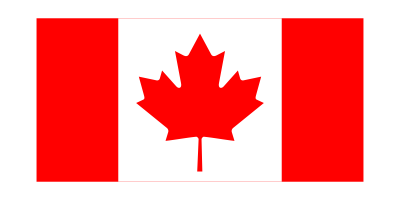


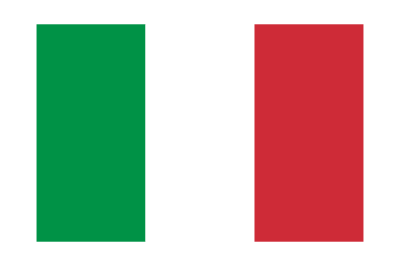




```mathematica
myCountryFlagList
```

```mathematica
ImageCollage[myCountryFlagList]
```

-Graphics-

```mathematica
(* Map的使用 *)
eList = Range[5]
```

{1,2,3,4,5}

```mathematica
Map[Factorial,eList] (* 这里的map类似于Python语言中map函数 *)
```

{1,2,6,24,120}

```mathematica
(* /@ 来使用Map的缩略形式 *)
Factorial /@ eList
```

{1,2,6,24,120}

```mathematica
? For
```

```mathematica
For[i=1,i<=5,i++,Print[i]]
```

1

2

3

4

5

```mathematica
(* 使用For循环来创建七国国旗的列表 *)
g7List = CountryData["G7"];
myFlagList = {};
For[i=1,i<=Length[g7List],i++,
AppendTo[myFlagList,CountryData[g7List[[i]],"Flag"]]
];
ImageCollage[myCountryFlagList]
```

-Graphics-

```mathematica
(* While 循环 *)
rn=1;
While[rn<=3,Print[rn];rn+=1](* 初始化-操作部分要与迭代器递增部分用分号隔开 *)
```

1

2

3

```mathematica
(* 使用For循环来创建七国国旗的列表 *)
g7List = CountryData["G7"];
myFlagList = {};
i=1;
While[i<=Length[g7List],
AppendTo[myFlagList,CountryData[g7List[[i]],"Flag"]];i+=1
];
ImageCollage[myCountryFlagList]
```

-Graphics-

```mathematica
(* Nest函数 返回对数据多次应用函数的结果 <函数，初始值，次数> *)
f[x_]:=x+1;
Nest[f,1,5]
```

6

```mathematica
f[x_]:=x*1.02;
Nest[f,1000,10]
```

1218.99

```mathematica
(* 对列表元素进行嵌套 *)
Nest[f,{500,10000,250000},10]
```

{609.497,12189.9,304749.}

```mathematica
(* 查看Nest嵌套的中间数值 *)
NestList[f,1000,10]
```

{1000,1020.,1040.4,1061.21,1082.43,1104.08,1126.16,1148.69,1171.66,1195.09,1218.99}

```mathematica
(* 在使用具有多个起始值的NestList的情况下，每一个步骤的中间值计算将被分到一起 *)
NestList[f,{500,10000,250000},10]
```

{{500,10000,250000},{510.,10200.,255000.},{520.2,10404.,260100.},{530.604,10612.1,265302.},{541.216,10824.3,270608.},{552.04,11040.8,276020.},{563.081,11261.6,281541.},{574.343,11486.9,287171.},{585.83,11716.6,292915.},{597.546,11950.9,298773.},{609.497,12189.9,304749.}}

```mathematica
MatrixForm[%70]
```

(500 | 10000 | 250000
510. | 10200. | 255000.
520.2 | 10404. | 260100.
530.604 | 10612.1 | 265302.
541.216 | 10824.3 | 270608.
552.04 | 11040.8 | 276020.
563.081 | 11261.6 | 281541.
574.343 | 11486.9 | 287171.
585.83 | 11716.6 | 292915.
597.546 | 11950.9 | 298773.
609.497 | 12189.9 | 304749.)

```mathematica
(* 模式匹配 *)
ReplaceAll[a x^2,a->4]
```

4 x^2

```mathematica
a x^2/. a->4
```

4 x^2

```mathematica
a x^2+ b x+c/.{a->2,b->3,c->4}
```

4+3 x+2 x^2

```mathematica
(* 基于模式匹配进行顺序的改变 *)
{a,b,c} /. {x_,y_,z_}->{y,x,z}
```

{b,a,c}



```mathematica
Graphics[Circle[{0,0},0.2]]
```

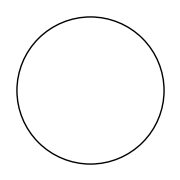

```mathematica
Show[Graphics[Circle[{0,0},0.2]],ImageSize->Small]
```

```mathematica
{-Graphics-,"This is a string",π} /. {x_,y_,z_}->{y,z,x}
```

{This is a string,π,-Graphics-}

```mathematica
{a,b,c} /. {x_,y_,z_}->x+y+z
```

a+b+c

```mathematica
{1,2,3} /. {x_,y_,z_}->x+y+z
```

6

```mathematica
(* 使用模式匹配构建新的列表 *)
{a,b,c}/.{x_,y_,z_}->{{x,x^2},{y,y^2},{z,z^2},{x+y+z,(x+y+z)}}
```

{{a,a^2},{b,b^2},{c,c^2},{a+b+c,a+b+c}}

```mathematica
{1,2,3}/. {x_,y_,z_}->{{x,x^2},{y,y^2},{z,z^2},{x+y+z,(x+y+z)^2}}
```

{{1,1},{2,4},{3,9},{6,36}}

```mathematica
(* 模式的特殊指定 *)
{2,2.5,π}/.x_Integer->x^2
```

{4,2.5,π}

```mathematica
(* 定义匹配特定标头的模式 *)
h[x_Integer]:=x;
h[x_Real]:=x^2;
h[x_Symbol]:=x^3;
h[x_String]:="This function dose not operate on Strings";
{h[1],h[1.1],h[π],h["test"]}
```

{1,1.21,π^3,This function dose not operate on Strings}

```mathematica
(* 条件函数 *)
? if
```

Missing[UnknownSymbol,if]

```mathematica
? If
```

```mathematica
If[π>3,"My test successed","My test failed"]
```

My test successed

```mathematica
If[π>3&&π>5,"My test successed","My test failed"]
```

My test failed

```mathematica
(* 使用多个测试的控制流 *)
Which[π>5,"Greater than 5",π>3,"Greater than 3",π>1,"Greater than 1"]
```

Greater than 3

```mathematica
(* 加入注释 *)
myFunction[x_]:=If[x<0,x,(* negative values remain the same *)x^2(* positive values are squared *)]
```

```mathematica
{myFunction[-2],myFunction[2]}
```

{-2,4}

```mathematica
Clear[listOfAllCountries,listOfCountries,countryDensity,countryList,countryList2,country,addSecondThird,x,f,myCountryFlagList,
myFlagList,myFunction,mylist,eList,G7,rn,h]
```